#### Problem description

```mathematica
Import["/Users/wenqiangfang/Dropbox (Brown)/Apps/OverLeafGit/StairStep/Figures/BeamSchematic_V10.png"]
```

-Graphics-

The governing equation for the Euler Elastica problem is

E I (d^2 θ)/(d s^2)+P_1 sin(θ)- P_2 cos(θ)=0

where 0≤s≤S is the arc length coordinate, θ is the angle of deflection (in radians) at point s, P_1 (positive when pointing to right) and P_2 (positive when pointing downward) are the horizontal and vertical forces at the left end of the beam, respectively.

We define θ as the angle from (ê)_1 to T̂ in the counter clockwise direction. (counter clockwise direction is the direction from (ê)_1 to (ê)_2.) We should have cos(θ) =T̂·(ê)_1

r(s)=x_1(s)(ê)_1+x_2(s) (ê)_2
T = (d r(s))/(d s)=x_1'(s)(ê)_1+x_2'(s) (ê)_2
||T||=√((x_1')^2+(x_2')^2)=1 (inextensibility)
T̂ =T/||T||=T
T̂·(ê)_1=x_1'(s)=cos(θ(s))
x_2'=sin(θ(s))
T=cos(θ(s))(ê)_1+sin(θ(s))(ê)_2
N=(d T(s))/(d s)=x_1''(s)(ê)_1+x_2''(s) (ê)_2
x_1''(s)=-sin(θ(s))θ'(s)
x_2''(s)=cos(θ(s))θ'(s)
||N|| = √((x_1'')^2+(x_2'')^2)=√((θ'(s))^2)=|θ'(s)| 
N̂=N/||N||=sign(θ'(s))(-sin(θ(s))(ê)_1+cos(θ(s)) (ê)_2)

The external force is P=P_1(ê)_1+P_2(ê)_2=P_n N̂-P_t T̂ and P_t=μ P_n.
In this case sign(θ'(s)) = -1, N̂=sin(θ(s))(ê)_1-cos(θ(s)) (ê)_2

P_1=P_n sin(θ_0)-μ P_n cos(θ_0)
P_2=-(P_n cos(θ_0)+μ P_n sin(θ_0))

Let ξ=2s/S, θ̂(ξ)=θ(s),  k=(P_n S^2)/(4 E I), g(ξ)=θ̂(ξ)-OverHat[θ_0]then the equation becomes

E I (d^2 θ)/(d s^2)+P_n(sin(θ_0)-μ  cos(θ_0))sin(θ)-P_n( cos(θ_0)+μ  sin(θ_0))cos(θ)=0
E I (d^2 θ)/(d s^2)-P_n(-cos(θ-θ_0)+μ  sin(θ-θ_0))=0
(d^2 θ̂(ξ))/(d ξ^2)=S^2/4(d^2 θ)/(d s^2)
(d^2 θ̂(ξ))/(d ξ^2)+k (cos(θ̂-OverHat[θ_0])-μ  sin(θ̂-OverHat[θ_0]))=0
(d^2 g(ξ))/(d ξ^2)+k (cos(g(ξ))-μ  sin(g(ξ)))=0

The simplified governing equation and boundary conditions are as follows

(d^2 g(ξ))/(d ξ^2)+k (cos(g(ξ))-μ  sin(g(ξ)))=0
g(ξ=0)=0
g'(ξ=0)=0
g(ξ=1)=-θ_0

where OverHat[θ_0]=θ̂(ξ=0)=θ(s=0)=θ_0>0, F=-2 P_2>0 is the magnitude of the reaction force.

And we also have

L=S∫_0^1 cos(θ̂(ξ)) dξ=S∫_0^1 cos(g-g(1)) dξ
w_0=S/2∫_0^1 sin(θ̂(ξ)) dξ=S/2∫_0^1 sin(g-g(1)) dξ
(P_n L^2)/(4 E I)=k (L/S)^2=(k(∫_0^1 cos(g-g(1)) dξ))^2
F=-2 P_2=2P_n(cos(θ_0)+μ sin(θ_0))
F̂=(F L^2)/(E I)=2P_n(cos(θ_0)+μ sin(θ_0))L^2/(E I)
= 8(cos(θ_0)+μ sin(θ_0))(P_n L^2)/(4E I)
=8(k(∫_0^1 cos(g-g(1)) dξ))^2(cos(θ_0)+μ sin(θ_0))
(ŵ)_0=w_0/L=1/2(∫_0^1 sin(g-g(1)) dξ)/(∫_0^1 cos(g-g(1)) dξ)

### Moment-deflection relations

k=(P L^2)/(E I)
V_0=-P (cos(θ_0)-μ sin(θ_0))
F=-2 V_0=2P(cos(θ_0)-μ sin(θ_0))
(F D^2)/(E I)=(P L^2)/(E I)2(cos(θ_0)-μ sin(θ_0))
(F D^2)/(E I)=2k (cos(θ_0)-μ sin(θ_0))
M=δ P_0-D V_0
...

### Numerical Procedure

```mathematica
μ=0.93;
```

```mathematica
δFCurve=ParallelTable[solg=NDSolve[{g''[ξ]+k( Cos[g[ξ]]-μ Sin[g[ξ]])==0,g[0]==0,g'[0]==0},g,{ξ,0,1}];
gsol[ξ_]=g[ξ]/.solg[[1]];
LS=NIntegrate[Cos[(gsol[ξ]-gsol[1])],{ξ,0,1}];
w0S=NIntegrate[Sin[(gsol[ξ]-gsol[1])],{ξ,0,1}]/2;
w0hat = w0S/LS;
Fhat = 8k(Cos[-gsol[1]]+μ Sin[-gsol[1]])LS^2;
{k,μ,1/LS,w0hat,Fhat,-gsol[1]},{k,0.02,3,0.02}];
```

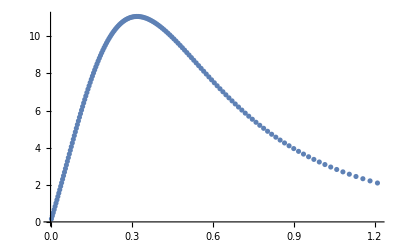

```mathematica
ListPlot[δFCurve[[;;,4;;5]]]
```

```mathematica
Isp=δFCurve[[Position[δFCurve[[;;,5]],Max[δFCurve[[;;,5]]]][[1]]]][[1]]
```

{1.52,0.93,1.22273,0.318801,11.066,0.835156}

```mathematica
SetDirectory[NotebookDirectory[]];
Save["dpCurveWithFriction",δFCurve]
```

```mathematica
SetDirectory[NotebookDirectory[]];
(*Get["dpCurveWithFriction"];*)
```

{1.52,0.93,1.22273,0.318801,11.066,0.835156}

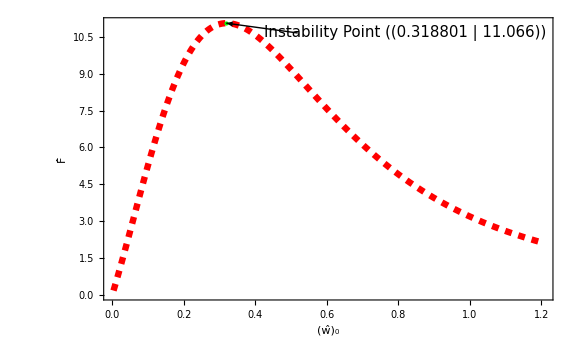

```mathematica
Isp=δFCurve[[Position[δFCurve[[;;,5]],Max[δFCurve[[;;,5]]]][[1]]]][[1]]
pIsp=Graphics[{PointSize[Large],Green,Point[Isp[[4;;5]]]}];
pArrow=Graphics[Arrow[{Isp[[4;;5]]+{0.2,-0.4},Isp[[4;;5]]}]];
ptext=Graphics[Text[Style["Instability Point "@{Isp[[4;;5]]},FontSize->15],Isp[[4;;5]]+{0.5,-0.4}]];
p1=ListPlot[δFCurve[[;;,4;;5]],Joined->True,PlotStyle->Directive[Red,Thickness[0.008],Dashed],PlotRange->Automatic,ImageSize->Large,GridLines->None,Ticks->Automatic,AxesStyle->Directive[Black,FontFamily->"Times",16],Frame->True,FrameStyle->Directive[FontFamily->"Times",12],FrameLabel->{Style["(ŵ)_0",Black,FontFamily->"Times",16],Style["F̂",Black,FontFamily->"Times",16]}];
Show[p1,pIsp,pArrow,ptext]
```

### Analytical solution

For the problem

θ''(s)+P̂ sin(θ(s))=0
θ(0)=0
θ(1)=0

For the current problem

(d^2 g(ξ))/(d ξ^2)+k (cos(g(ξ))-μ  sin(g(ξ)))=0
g(ξ=0)=0
g'(ξ=0)=0
g(ξ=1)=-θ_0

We can write it as equation of β(ξ)=g(ξ)+g_0, where sin(g_0)=1/(√(1+μ^2)),cos(g_0)=-μ/(√(1+μ^2))

(d^2 β(ξ))/(d ξ^2)+k √(1+μ^2) sin(β)=0
β(ξ=0)=g_0=arccos(-μ/(√(1+μ^2)))
β'(ξ=0)=0

```mathematica
β[s_,p_,κ_]=2 ArcSin[√κ JacobiCD[√p s,κ]];
IntCos[p_,κ_]:=1-(2 (√p-EllipticE[JacobiAmplitude[√p,κ],κ]) JacobiDN[√p,κ])/(√p √(1-κ JacobiSN[√p,κ]^2))-(2 √2 κ JacobiCN[√p,κ] JacobiDN[√p,κ] JacobiSN[√p,κ])/(√p √(1-κ JacobiSN[√p,κ]^2) √(2-κ+κ JacobiCN[√p,κ]^2-κ JacobiSN[√p,κ]^2));
IntSin[p_,κ_]:=-((2 (-1+κ JacobiSN[√p,κ]^2)^2 ((-1+κ) EllipticE[ArcSin[(√(2-κ+κ JacobiCN[√p,κ]^2-κ JacobiSN[√p,κ]^2))/(√2)],(-1+JacobiDN[√p,κ]^2/(1-κ JacobiSN[√p,κ]^2))/(-1+κ)] JacobiNS[√p,κ] √(-κ JacobiSN[√p,κ]^2 (-2+κ-κ JacobiCN[√p,κ]^2+κ JacobiSN[√p,κ]^2)) √(1/((-1+κ) (-1+κ JacobiSN[√p,κ]^2))(-κ (-1+JacobiSN[√p,κ]^2) (-1+κ JacobiSN[√p,κ]^2)-JacobiDN[√p,κ]^2 (-2+κ+κ JacobiSN[√p,κ]^2)+κ JacobiCN[√p,κ]^2 (-1+JacobiDN[√p,κ]^2+κ JacobiSN[√p,κ]^2)))-1/(-1+κ JacobiSN[√p,κ]^2)EllipticF[ArcSin[(√(2-κ+κ JacobiCN[√p,κ]^2-κ JacobiSN[√p,κ]^2))/(√2)],(-1+JacobiDN[√p,κ]^2/(1-κ JacobiSN[√p,κ]^2))/(-1+κ)] JacobiNS[√p,κ] √(-κ JacobiSN[√p,κ]^2 (-2+κ-κ JacobiCN[√p,κ]^2+κ JacobiSN[√p,κ]^2)) (JacobiDN[√p,κ]^2+κ (-1+κ JacobiSN[√p,κ]^2)) √(1/((-1+κ) (-1+κ JacobiSN[√p,κ]^2))(-κ (-1+JacobiSN[√p,κ]^2) (-1+κ JacobiSN[√p,κ]^2)-JacobiDN[√p,κ]^2 (-2+κ+κ JacobiSN[√p,κ]^2)+κ JacobiCN[√p,κ]^2 (-1+JacobiDN[√p,κ]^2+κ JacobiSN[√p,κ]^2)))+κ JacobiSN[√p,κ] (κ+((-2+κ) JacobiDN[√p,κ]^2)/(1-κ JacobiSN[√p,κ]^2)-κ (JacobiCN[√p,κ]^2-JacobiSN[√p,κ]^2) (-1+JacobiDN[√p,κ]^2/(1-κ JacobiSN[√p,κ]^2)))))/(√p √κ JacobiDN[√p,κ]^4 (2-κ+κ JacobiCN[√p,κ]^2-κ JacobiSN[√p,κ]^2) √((-κ (-1+JacobiSN[√p,κ]^2) (-1+κ JacobiSN[√p,κ]^2)-JacobiDN[√p,κ]^2 (-2+κ+κ JacobiSN[√p,κ]^2)+κ JacobiCN[√p,κ]^2 (-1+JacobiDN[√p,κ]^2+κ JacobiSN[√p,κ]^2))/(JacobiDN[√p,κ]^2 (2-κ+κ JacobiCN[√p,κ]^2-κ JacobiSN[√p,κ]^2)))));
```

```mathematica
NumSol[μ_,k_]:=Module[{g,solg,gsol,LS,w0S,w0hat,Fhat},solg=NDSolve[{g''[ξ]+k( Cos[g[ξ]]-μ Sin[g[ξ]])==0,g[0]==0,g'[0]==0},g,{ξ,0,1}];
gsol[ξ_]=g[ξ]/.solg[[1]];
LS=NIntegrate[Cos[(gsol[ξ]-gsol[1])],{ξ,0,1}];
w0S=NIntegrate[Sin[(gsol[ξ]-gsol[1])],{ξ,0,1}]/2;
w0hat = w0S/LS;
Fhat = 8k(Cos[-gsol[1]]+μ Sin[-gsol[1]])LS^2;
{k,μ,1/LS,w0hat,Fhat,-gsol[1]}]
```

```mathematica
AnaSol[μ_,k_]:=Module[{p,kn,g0,Solkn,β1,knReal,gsol,LS,w0S,w0hat,Fhat},
p = k Sqrt[1+μ^2];
g0 = ArcCos[-μ/Sqrt[1+μ^2]];
knReal=1/2 (1+μ/(√(1+μ^2)));
β1=β[1,p,knReal];
gsol[s_]:=β[s,p,knReal]-g0;
LS = Cos[β1] IntCos[p,knReal]+Sin[β1]IntSin[p,knReal];
w0S = (Cos[β1] IntSin[p,knReal]-Sin[β1]IntCos[p,knReal])/2;
w0hat =w0S/LS;
Fhat = 8k(Cos[-gsol[1]]+μ Sin[-gsol[1]])LS^2;
Re@{w0hat,Fhat,k,-gsol[1],1/LS,μ}]
```

```mathematica
SolutionVector2 = ParallelTable[sol = AnaSol[μ,k];
If[sol[[4]]<π/2,sol,Null],{k,0.001,1.5,0.0005},{μ,0.1,0.5,0.0005}];
```

```mathematica
SetDirectory[NotebookDirectory[]];
DumpSave["data/SolutionVector2_Dec5.mx",SolutionVector2]
```

{{{{0.000166668,0.0080004,0.001,0.000500004,1.,0.1},{0.000166668,0.0080004,0.001,0.000500004,1.,0.1005},{0.000166668,0.0080004,0.001,0.000500004,1.,0.101},795,{0.000166675,0.00800199,0.001,0.000500021,1.,0.499},{0.000166675,0.008002,0.001,0.000500021,1.,0.4995},{0.000166675,0.008002,0.001,0.000500021,1.,0.5}},2997,{{0.270986,4,0.1},799,{1}}}}
 |  |  |  |

For the instability point, we have

(d F̂)/(d k)=0
(d(8(k(∫_0^1 cos(g-g(1)) dξ))^2(cos(θ_0)+μ sin(θ_0))))/(d k)=0
k(∫_0^1 cos(g-g(1)) dξ)^2(cos(θ_0)+μ sin(θ_0))+k

```mathematica
SolutionVector2=Table[ParallelTable[solg=NDSolve[{g''[ξ]-k( Cos[g[ξ]]-μ Sin[g[ξ]])==0,g[0]==0,g'[0]==0},g,{ξ,0,1}];
θ[ξ_]=-(g[ξ]-g[1])/.solg[[1]];
θ0=g[ξ]/.solg[[1]]/.ξ->1;
If[θ0<π/2,
IntSinθ=NIntegrate[Sin[θ[ξ]],{ξ,0,1}];
IntCosθ=NIntegrate[Cos[θ[ξ]],{ξ,0,1}];
w=IntSinθ/(2IntCosθ);
F=8k IntCosθ^2( Cos[θ0]+μ  Sin[θ0]);
{w,F,k,θ0,1/IntCosθ,μ}],{k,0.001,5,0.002}],{μ,0.0,1.0,0.002}];
```

```mathematica
SetDirectory[NotebookDirectory[]];
Get<<"SolutionVector2_Feb3";
SolutionVector3=SolutionVector2/.Null->Nothing;
```

SolutionVector2 = {OverHat[w_0], F̂, k, θ_0, Ŝ, μ}

```mathematica
kLen =Range[0.001,5,0.002]//Dimensions
μLen =Range[0.0,1.0,0.002]//Dimensions
```

{2500}

{501}

```mathematica
SolutionVector3//Dimensions
```

{501}

```mathematica
fitFw0B=Module[{data1,fit},
Table[
data1=SolutionVector3[[n,;;,{1,2}]];
fit[x_]=Fit[data1,{x,x^2,x^3,x^4,x^5,x^6},x];
Function[x,Evaluate@fit[x]]
,{n,1,Length@SolutionVector3}]
];
Isps=Table[SolutionVector3[[n,Position[SolutionVector3[[n,;;,2]],Max[SolutionVector3[[n,;;,2]]]][[1]]]][[1]]
,{n,Length@SolutionVector3}];
EndPoints = SolutionVector3[[;;,-1,1]];
EndPointsList=Table[{EndPoints[[n]],fitFw0B[[n]][EndPoints[[n]]]},{n,1,Length@EndPoints}];
```

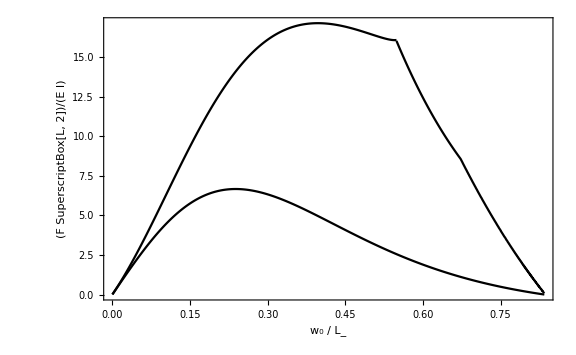

```mathematica
p11=ListPlot[SolutionVector3[[{1,-1},;;,{1,2}]],Joined->True,
PlotStyle->Black,
ImageSize->Large,GridLines->None,Ticks->Automatic,PlotRange->Automatic,
AxesStyle->Directive[Black,FontFamily->"Times",28],Frame->True,FrameStyle->Directive[Black,FontFamily->"Times",16],FrameLabel->{Style["w_0 / L_",Black(*,Italic*),FontFamily->"Times",16],Style["(F SuperscriptBox[L, 2])/(E I)",Black,FontFamily->"Times",16]},RotateLabel->False];
p12=ListPlot[EndPointsList,Joined->True,PlotStyle->Black,
ImageSize->Large,GridLines->None,Ticks->Automatic,PlotRange->Automatic,
AxesStyle->Directive[Black,FontFamily->"Times",28],Frame->True,FrameStyle->Directive[Black,FontFamily->"Times",16],FrameLabel->{Style["w_0 / L_",Black(*,Italic*),FontFamily->"Times",16],Style["(F SuperscriptBox[L, 2])/(E I)",Black,FontFamily->"Times",16]},RotateLabel->False];
p1 =Show[p11,p12]
```

```mathematica
PhaseBoundary[kc_] := Module[{SIspsw0,Xroot,Xresidual,SIspsw0Eff,SIspsF,EndInd,pb},
SIspsw0=Table[
Off[FindRoot::lstol];
Xroot =FindRoot[D[fitFw0B[[n]][x],x]+kc,{x,Isps[[n,1]]}];
Xresidual = D[fitFw0B[[n]][x],x]+kc/.Xroot;
If[Abs@Xresidual<10^-6&&0≤(x/.Xroot)≤EndPoints[[n]],x/.Xroot]
,{n,Length@fitFw0B}];
SIspsw0Eff=SIspsw0/.Null->Nothing;
EndInd =Length@SIspsw0Eff;
SIspsF=Table[fitFw0B[[n]][SIspsw0Eff[[n]]],{n,1,Length@SIspsw0Eff}];
pb=ListPlot[Transpose[{SIspsw0Eff,SIspsF}],Joined->True,
PlotStyle->Blue];
Print[SolutionVector3[[EndInd,1,6]]];
If[EndInd==Length@SIspsw0,
pb,
Show[pb,ListPlot[SolutionVector3[[EndInd,;;,{1,2}]],Joined->True,
PlotStyle->{Dashed,Black}]]
]
];
```

```mathematica
PhaseBoundary/@{0,10,15,18,22};
```

1.

0.998

0.956

0.544

2

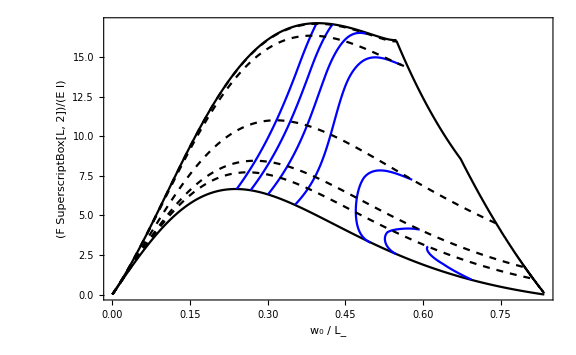

```mathematica
SlopeList = {0,5,10,15,18,20,22};
PBS = PhaseBoundary/@SlopeList;
```

```mathematica
OblSlope
```

{80.5738,79.1088,53.0608,98.8861,55.7819,101.186,88.7956,127.97,54.3873,108.775,96.6886,255.94,62.157,50.5929,167.346,60.4304,67.9842,62.157,81.3465,70.5003,69.9665,109.57}

```mathematica
PhaseDiagram=Show[p1,PBS]
```

-Graphics-

```mathematica
SetDirectory[NotebookDirectory[]];
Export["PhaseDiagram.EPS",PhaseDiagram]
```

PhaseDiagram.EPS